Limits, difference quotient, derivatives

```mathematica
Clear[x0];
Clear[h];
```

```mathematica
x0:=2
h := x0 + 1
```

```mathematica
f = x0^2;
```

```mathematica
(f(x0+h) - f(x0)) /  ((x0 + h) - x0)
```

4

```mathematica
(* (x0+h)^2 is x0^2 + 2x0 * h + h^2) *)
((x0^2+(2x0*h)+h^2)-x0^2) / h
```

7

```mathematica
(* x0^2 cancels in the numerator, and x0 cancels in the denominator *)((2x0*h)+h^2)/h
```

7

```mathematica
(* Divide BOTH numerators with the denominator *)
```

```mathematica
2x0+h
```

7

```mathematica
h:=0 (* As h->0, we get answer 2x, which is the derivative of x^2 *)
2x0+h
```

4

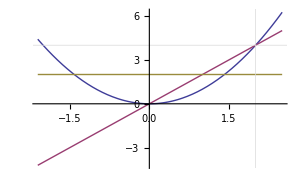

```mathematica
Clear[f];
Clear[x0];
f[x0_] = x0^2;
Plot[{f[x], f'[x], f''[x]}, {x, -2.1, 2.5}, GridLines->{{2},{4}},
GridLinesStyle->LightGray]
```

```mathematica
Clear[x];
f[x_] = x^2;
x0=2;
h=0.000001;
(* Difference quotient and h->0, compared to derivative *)
{(f[x0+h] - f[x0]) /  ((x0 + h) - x0), f'[x0]}
```

{4.,4}

```mathematica
Clear[x];
f[x_] = 1/x;
x0=1.2;
h=0.0000001;
(* Difference quotient and h->0, compared to derivative *)
{N[(f[x0+h] - f[x0]) /  ((x0 + h) - x0)], N[f'[x0]]}
```

{-0.694444,-0.694444}

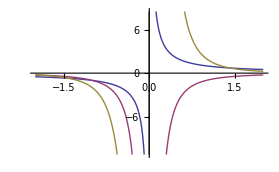

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -2, 2}]
```

```mathematica
Clear[x];
f[x_] = Sin[x^3];
x0=1.2;
h=0.0000001;
(* Difference quotient and h->0, compared to derivative *)
{N[(f[x0+h] - f[x0]) /  ((x0 + h) - x0)], N[f'[x0]]}
```

{-0.676327,-0.676326}

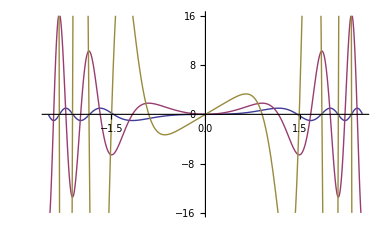

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -2.5, 2.5}, PlotRange->{{-2.5,2.5},{-16,16}}]
```